```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
rawDataRR=Import["rrTrace.txt","Table"];
npart = rawDataRR[[2,1]];
nd = rawDataRR[[2,2]];
βRR = rawDataRR[[2,3]];
ωRR = rawDataRR[[2,4]];
nbead = rawDataRR[[2,5]];
datasRR = Table[rawDataRR[[n]],{n,3,Length[rawDataRR]}];
```

```mathematica
For[i=1,i<=nbead,i++,dataRR[i]=Table[datasRR[[n,i]],{n,1,Length[datasRR]}]];
For[i=1,i<=nbead,i++,stdErrRR[i] = StandardDeviation[dataRR[i]]/√Length[dataRR[i]]]
```

```mathematica
pointsRR=Table[{{i-1,Mean[dataRR[i]]},ErrorBar[stdErrRR[i]]},{i,1,nbead}];
```

```mathematica
c[j_,β_,ω_,d_,τ_]:=d/(2ω)(Cosh[(β ω)/2-τ j ω]/Sinh[(β ω)/2]);
```

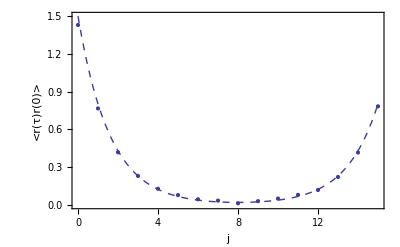

```mathematica
modelRRPlot=Plot[c[j,βRR,ωRR,nd,βRR/nbead],{j,0,nbead-1},PlotStyle->Dashed];
pointsRRPlot=ErrorListPlot[pointsRR,PlotStyle->Thick];
Show[modelRRPlot,pointsRRPlot,LabelStyle->Directive[FontFamily->"Helvetica"],Frame->True,FrameLabel-> {Style["j",Bold],Style["<r(τ)r(0)>",Bold]}]
```